# Begynnelsevärdesproblem

## Exempel från föreläsningen

### Exempel 1

```mathematica
DSolve[y'[x]==2x*y[x],y[x],x]
```

{{y[x]→ⅇ^(x^2) C[1]}}

### Exempel 2

```mathematica
DSolve[{y'[x]==2x*y[x],y[0]==1},y[x],x]
```

{{y[x]→ⅇ^(x^2)}}

### Exempel 3 (Taylorutveckling)

Taylor: y_T(x) = x-x^3,  Mathematica: y_M(x) = ⅇ^(-(3 x^2)/2) √(π/6) Erfi[√(3/2) x]

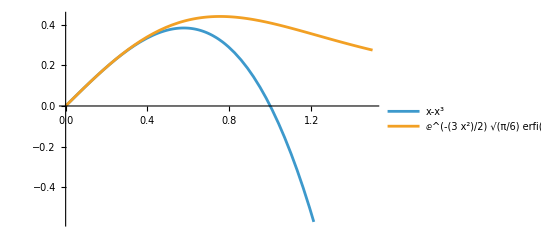

```mathematica
Remove["Global`*"]
ode=y'[x]==1-3x*y[x];
{x0,y0}={0,0};
xmax=1.5;
ordn=3;
dlist={ode};
For[i=1,i<ordn,++i,
AppendTo[dlist,D[dlist[[i]],x]];
]
deriv=Solve[dlist/.x->x0/.y[0]->y0];
yT=Normal[Series[y[x],{x,0,ordn}]/.deriv/.y[0]->y0][[1]];
yM=y[x]/.First[DSolve[{ode,y[x0]==y0},y[x],x]];
Print["Taylor: y_T(x) = ",yT,",  Mathematica: y_M(x) = ",yM]
pl=Plot[{yT,yM},{x,x0,xmax},PlotLegends->"Expressions"]
```

### Exempel 4 (Eulers metod)

0.183202

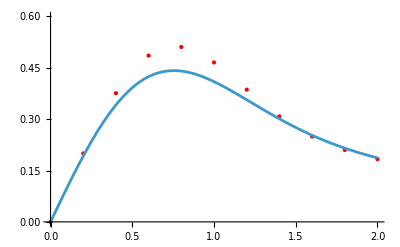

```mathematica
Remove["Global`*"]
{a,b}={0,2.};
{x0,y0}={0,0};
n=10;
h=(b-a)/n;
f[x_,y_]=1-3x*y;
dlist= {{xold,yold}}={{x0,y0}};
For[i=0,i<n,++i,
xnew=xold+h;
ynew=yold+ h*f[xold,yold];
AppendTo[dlist,{xnew,ynew}];
xold=xnew;
yold=ynew;
]
yM=y[x]/.First[DSolve[{y'[x]==(f[x,y]/.y->y[x]),y[x0]==y0},y[x],x]];
lp=ListPlot[dlist,PlotStyle->{Red,PointSize[Medium]},PlotRange->{0,0.6}];
pl=Plot[yM,{x,a,b},PlotRange->{0,0.5}];
Show[lp,pl]
```

### Exempel 5 (Heuns metod)

0.191071

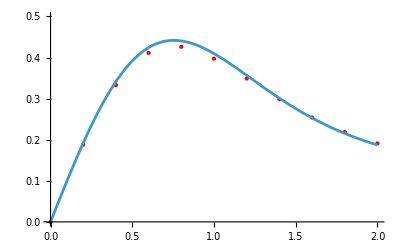

```mathematica
Remove["Global`*"]
{a,b}={0,2.};
{x0,y0}={0,0};
n=10;
h=(b-a)/n;
f[x_,y_]=1-3x*y;
dlist= {{xold,yold} }={{x0,y0}};
For[i=0,i<n,++i,
xnew=xold+h;
k1=h*f[xold,yold];
k2=h*f[xold+h,yold+k1];
ynew=yold+(1/2)*(k1+k2);
AppendTo[dlist,{xnew,ynew}];
xold=xnew;
yold=ynew;
]
yM=y[x]/.First[DSolve[{y'[x]==(f[x,y]/.y->y[x]),y[x0]==y0},y[x],x]];
lp=ListPlot[dlist,PlotStyle->{Red,PointSize[Medium]},PlotRange->{0,0.5}];
pl=Plot[yM,{x,a,b},PlotRange->{0,0.5}];
Show[lp,pl]
```

### Exempel 6 (Heuns metod)

0.188942

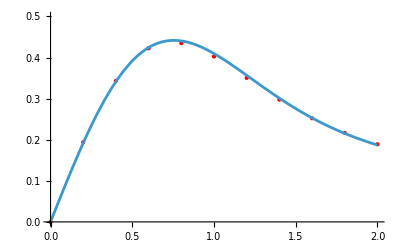

```mathematica
Remove["Global`*"]
{a,b}={0,2.};
{x0,y0}={0,0};
n=10;
h=(b-a)/n;
f[x_,y_]=1-3x*y;
dlist= {{xold,yold}}={{x0,y0}};
For[i=0,i<n,++i,
xnew=xold+h;
k1=h*f[xold,yold];
ynew=yold+h*f[xold+h/2,yold+k1/2];
AppendTo[dlist,{xnew,ynew}];
xold=xnew;
yold=ynew;
]
yM=y[x]/.First[DSolve[{y'[x]==(f[x,y]/.y->y[x]),y[x0]==y0},y[x],x]];
lp=ListPlot[dlist,PlotStyle->{Red,PointSize[Medium]},PlotRange->{0,0.5}];
pl=Plot[yM,{x,a,b},PlotRange->{0,0.5}];
Show[lp,pl]
```

### Exempel 7 (Runge-Kutta)

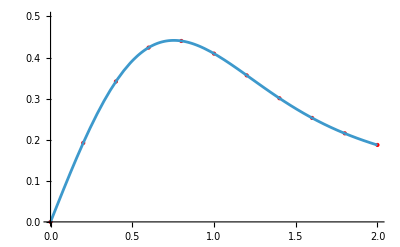

```mathematica
Remove["Global`*"]
{a,b}={0,2.};
{x0,y0}={0,0};
n=10;
h=(b-a)/n;
f[x_,y_]=1-3x*y;
dlist= {{xold,yold}}={{x0,y0}};
ak=1/6{1,2,2,1};
For[i=0,i<n,++i,
xnew=xold+h;
k1=h*f[xold,yold];
k2=h*f[xold+h/2,yold+k1/2];
k3=h*f[xold+h/2,yold+k2/2];
k4=h*f[xold+h,yold+k3];
ynew=yold+ak.{k1,k2,k3,k4};
AppendTo[dlist,{xnew,ynew}];
xold=xnew;
yold=ynew;
]
yM=y[x]/.First[DSolve[{y'[x]==(f[x,y]/.y->y[x]),y[x0]==y0},y[x],x]];
lp=ListPlot[dlist,PlotStyle->{Red,PointSize[Medium]},PlotRange->{0,0.5}];
pl=Plot[yM,{x,a,b},PlotRange->{0,0.5}];
Show[lp,pl]
```

### Exempel 8 (Implicit Euler)

0.188986

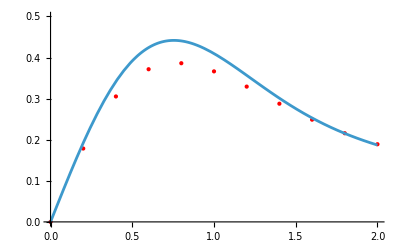

```mathematica
Remove["Global`*"]
{a,b}={0,2.};
{x0,y0}={0,0};
n=10;
h=(b-a)/n;
f[x_,y_]=1-3x*y;
dlist= {{xold,yold}}={{x0,y0}};
For[i=0,i<n,++i,
xnew=xold+h;
ynew=yn/.First[Solve[yn==yold+ h*f[xnew,yn],yn]];
AppendTo[dlist,{xnew,ynew}];
xold=xnew;
yold=ynew;
]
yM=y[x]/.First[DSolve[{y'[x]==(f[x,y]/.y->y[x]),y[x0]==y0},y[x],x]];
lp=ListPlot[dlist,PlotStyle->{Red,PointSize[Medium]},PlotRange->{0,0.5}];
pl=Plot[yM,{x,a,b},PlotRange->{0,0.5}];
Show[lp,pl]
```

### Exempel 8 (Implicit Mittpunktsmetod)

0.186082

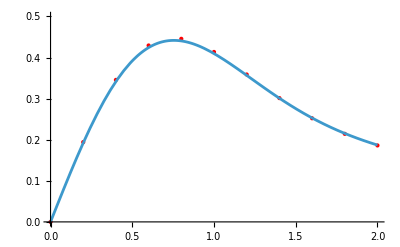

```mathematica
Remove["Global`*"]
{a,b}={0,2.};
{x0,y0}={0,0};
n=10;
h=(b-a)/n;
f[x_,y_]=1-3x*y;
dlist= {{xold,yold}}={{x0,y0}};
For[i=0,i<n,++i,
xnew=xold+h;
ynew=yn/.First[Solve[yn==yold+ h*f[(xold+xnew)/2,(yold+yn)/2],yn]];
AppendTo[dlist,{xnew,ynew}];
xold=xnew;
yold=ynew;
]
yM=y[x]/.First[DSolve[{y'[x]==(f[x,y]/.y->y[x]),y[x0]==y0},y[x],x]];
lp=ListPlot[dlist,PlotStyle->{Red,PointSize[Medium]},PlotRange->{0,0.5}];
pl=Plot[yM,{x,a,b},PlotRange->{0,0.5}];
Show[lp,pl]
```